```mathematica
{θ''[t] == Sin[2θ[t]] - Sin[θ[t]], θ[0]==Pi, θ'[t] == 0}
```

{θ''[t]==-Sin[θ[t]]+Sin[2 θ[t]],θ[0]==π,θ'[t]==0}

```mathematica
θ[t]/.Flatten[NDSolve[{θ''[t]==5Sin[2θ[t]]-Sin[ θ[t]],θ[0]==Pi-0.6,θ'[0]==0},{θ[t]},{t,0,30}]]
```

InterpolatingFunction[…][t]

```mathematica
Plot[%32,{t,0.,30.}, AxesLabel->{"t", "θ(t)"}]
```

-Graphics-

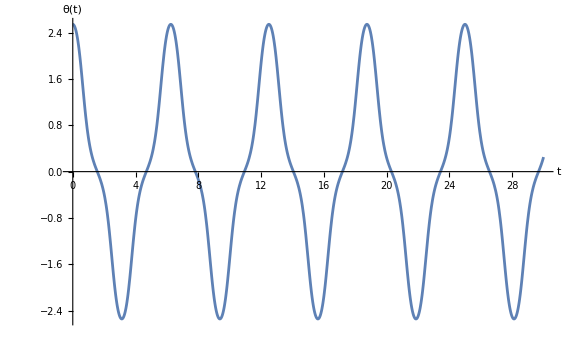

```mathematica
Show[%34,ImageSize->Large]
```

```mathematica
Plot[%29,{t,0.,30.}]
```

-Graphics-

```mathematica
Plot[%27,{t,0.,30.}]
```

-Graphics-

```mathematica
Plot[%25,{t,0.,30.}]
```

-Graphics-

```mathematica
Plot[%22,{t,0.,10.}]
```

-Graphics-

```mathematica
Plot[%20,{t,0.,10.}]
```

-Graphics-

```mathematica
Plot[%17,{t,0.,10.}]
```

-Graphics-

```mathematica
Plot[[x],x⟦InterpolatingFunction[{{0.,10.}},{5,7,2,{107},{4},0,0,0,0,Automatic,{},{},False},{{0.,0.00014373663366825222,0.00028747326733650445,0.0034814841092491093,0.006675494951161714,0.009869505793074319,0.010103896068842383,0.010338286344610446,0.01057267662037851,0.010807066896146574,0.011041457171914638,0.011510237723450766,0.011979018274986894,0.012447798826523021,0.017135604341884297,0.021823409857245575,0.026511215372606853,0.03119902088796813,0.06792883806500644,0.10465865524204473,0.14138847241908303,0.17811828959612136,0.21484810677315966,0.2583824988556481,0.3019168909381366,0.34545128302062506,0.38898567510311355,0.43252006718560204,0.4760544592680905,0.5358663490744796,0.5956782388808687,0.6554901286872578,0.7153020184936468,0.7751139083000359,0.834925798106425,0.8947376879128142,0.9545495777192032,1.0143614675255923,1.0741733573319814,1.1467275690390797,1.2192817807461778,1.2783177444063092,1.3373537080664406,1.396389671726572,1.4554256353867037,1.514461599046835,1.5734975627069665,1.632533526367098,1.7019679060415844,1.771402285716071,1.8408366653905575,1.910271045065044,1.9797054247395305,2.049139804414017,2.1185741840885033,2.18800856376299,2.2574429434374763,2.326877323111963,2.3963117027864493,2.465746082460936,2.5351804621354224,2.623976185518004,2.7127719089005855,2.801567632283167,2.890363355665749,2.9791590790483307,3.0679548024309122,3.156750525813494,3.2641482744631194,3.371546023112745,3.478943771762371,3.5863415204119966,3.693739269061622,3.801137017711248,3.908534766360874,4.015932515010499,4.159731430385322,4.3035303457601435,4.447329261134966,4.591128176509788,4.73492709188461,4.8787260072594325,5.022524922634255,5.166323838009077,5.310122753383899,5.510125040808328,5.710127328232756,5.910129615657184,6.110131903081613,6.310134190506042,6.51013647793047,6.710138765354898,6.910141052779327,7.110143340203756,7.3101456276281835,7.510147915052612,7.7356053295846765,7.96106274411674,8.186520158648804,8.411977573180868,8.637434987712933,8.862892402244997,9.08834981677706,9.338349691132457,9.588349565487855,9.794174782743928,10.}},{Developer`PackedArrayForm,{0,3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81,84,87,90,93,96,99,102,105,108,111,114,117,120,123,126,129,132,135,138,141,144,147,150,153,156,159,162,165,168,171,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,225,228,231,234,237,240,243,246,249,252,255,258,261,264,267,270,273,276,279,282,285,288,291,294,297,300,303,306,309,312,315,318,321},{1.5707963267948966,0.,-0.9999999999999999,1.5707963061346768,-0.00014373662772899129,-0.99999995867956,1.5707962648142397,-0.0002874732435794611,-0.9999998760386827,1.5707902458002792,-0.0034814644646498014,-0.9999878379402386,1.5707740252571807,-0.006675384651770453,-0.9999553965718281,1.5707476035158923,-0.009869168637023503,-0.9999025521510895,1.5707452353455402,-0.010103534961807763,-0.9998978157957885,1.5707428122422669,-0.010337900150658632,-0.9998929694625206,1.5707403342063448,-0.010572264177822657,-0.9998880132550131,1.570737801238052,-0.010806627017546418,-0.9998829471734131,1.5707352133376729,-0.011040988644076533,-0.9998777712178726,1.570729927673329,-0.011509709419241272,-0.9998671995528092,1.5707244222829935,-0.011978425135601389,-0.9998561883915116,1.57071869716908,-0.012447135587130013,-0.9998447377357629,1.5706493618503052,-0.017133906241613397,-0.9997060592989339,1.5705580575681535,-0.021819922930483165,-0.999523433195214,1.5704447883190675,-0.026504980498334642,-0.9992968613166245,1.5703095590817393,-0.031188872941725752,-0.9990263462560797,1.5684907885986286,-0.06782433257828796,-0.9953862822198127,1.5653294497191452,-0.10427659523733807,-0.9890515208396945,1.5608341126429424,-0.14044677128197686,-0.9800272685085097,1.555016942095287,-0.1762362203293351,-0.9683219781993585,1.5478937279717275,-0.2115466900354761,-0.9539485667728446,1.5377863604163369,-0.2526442232534576,-0.9334832405592199,1.5259103961856901,-0.29277058374318843,-0.9093414655707478,1.512311578843582,-0.33176704830129106,-0.8815873028519137,1.4970424956132373,-0.3694781582559125,-0.8503081012775096,1.4801624102071325,-0.4057528466079761,-0.8156187805675686,1.4617370442306887,-0.4404457223385973,-0.7776657799682162,1.4340353455266626,-0.4852785895717385,-0.7205386490734933,1.4037575153472743,-0.5265349449744188,-0.6581834996242435,1.3711264038255002,-0.5639230227522555,-0.5913218699757149,1.3363809512263827,-0.5971981627415263,-0.5208067795508713,1.2997731346610777,-0.6261703007595114,-0.4476073506736286,1.2615645059086236,-0.6507102056537967,-0.3727835546574311,1.222022410500211,-0.670753934019414,-0.2974521904924484,1.1814160047117157,-0.6863050472607417,-0.22274666775699212,1.140012213790396,-0.697434319695101,-0.14977379440954253,1.0980717851254855,-0.7042768609767518,-0.07957117397052305,1.0468357400338362,-0.707106397821108,0.0005425408579771139,0.9955995475762842,-0.7043633366273414,0.07383934624980404,0.954177538874043,-0.6983868503652313,0.12772756861454151,0.913199075044115,-0.6893919780695589,0.17604819703746724,0.8728325008690878,-0.6777142008782301,0.21859705008519173,0.8332260981063891,-0.6636964775247444,0.2553237198720042,0.7945078927104516,-0.6476805859064592,0.2863151251761643,0.7567859574978336,-0.6299996217240074,0.3117748920510599,0.7201491127070616,-0.610971775108723,0.3320004309068821,0.6785423969640033,-0.587271774466866,0.3495915101019106,0.6386186781600133,-0.5625644777261914,0.3611331940549489,0.6004338927498309,-0.5372448318757459,0.3673526567160363,0.5640183225434141,-0.5116567759013275,0.3689863175272185,0.5293801318070901,-0.4860936730266803,0.3667503216492063,0.49650881168911154,-0.460800507547901,0.3613190909555438,0.46537842603696045,-0.4359773126357066,0.35331116730183965,0.43595059031728134,-0.41178336009722466,0.3432812127528368,0.4081771445242358,-0.3883417283337469,0.33171690590075026,0.38200250461002816,-0.3657439516370228,0.31903950640125783,0.3573656947231985,-0.3440545351611728,0.305606990389364,0.3342020750016426,-0.32331519006142,0.2917188377822434,0.3124447877106669,-0.30354870048477695,0.277621742922821,0.28656171518263535,-0.27969825626469785,0.25960320485238675,0.2627257341744074,-0.2574362694531372,0.2418899038119192,0.24079733421381438,-0.23672464559683806,0.22471601967410984,0.22064121086564165,-0.21750780050541904,0.20824405492648154,0.20212755705860608,-0.19971833279069715,0.1925799993465097,0.18513290730928952,-0.18328145855206596,0.1777860759638923,0.16954063503492786,-0.16811841626105575,0.1638912282388665,0.15239966045360112,-0.15136631615988622,0.14829134070481442,0.13697035847889197,-0.1362197713378104,0.1339848273089532,0.12308767001074762,-0.12254252309370635,0.12091929565403936,0.11060082747771142,-0.1102048448065092,0.10902667615629398,0.0993725831617229,-0.09908483437200756,0.09823023784645515,0.08927833022347034,-0.08906906579186587,0.08844958916707905,0.08020517795254688,-0.08005278457239075,0.07960409322798224,0.07205102460225643,-0.07193980456167169,0.07161514301925255,0.06241276277545794,-0.06233939898120523,0.06212936628502402,0.054061345900820686,-0.054012431042787974,0.05387712796418738,0.0468258687379856,-0.04679265630307943,0.04670614423764479,0.04055781321165617,-0.04053458497192257,0.04048001127951681,0.035128226217008326,-0.0351112313718435,0.03507766960742041,0.030425213946212712,-0.03041197524107599,0.030392363032007902,0.02635173223813887,-0.026340594568681142,0.02633038671699331,0.022823645432806274,-0.022813480852424895,0.02280977650169131,0.019768030977831277,-0.01975804574697165,0.019759019566356187,0.01618651914395225,-0.01617583895522209,0.01618157195981448,0.013254439143958505,-0.013242227073267332,0.013251724207177053,0.010854205976982887,-0.010839746936587893,0.010852715963529725,0.00888953854938615,-0.008872128821806899,0.008888719855636384,0.007281613695597854,-0.007260487197952,0.007281163683138295,0.005965913670401879,-0.0059401853941705544,0.005965666304051107,0.004889641925952064,-0.0048582589619531975,0.004889505893102254,0.004009607458085706,-0.0039712991293110265,0.00400953262949329,0.003290493197728735,-0.003243715849897006,0.0032904519475459473,0.0027034392534123755,-0.0026463121618979756,0.002703416467577669,0.0022248853284101903,-0.0021551138850737,0.00222487270886484,0.0017916587713602823,-0.0017042448232495457,0.0017916524175306755,0.001449889617046528,-0.0013403703053224826,0.001449886791436962,0.001182131877115673,-0.0010449162567597297,0.0011821297279332162,0.0009747184540974765,-0.0008028019318162856,0.000974716191012013,0.0008170613909422216,-0.0006016680915088928,0.0008170596725877122,0.0007011127150474587,-0.0004312474536154575,0.0007011113542313042,0.0006209536689039304,-0.00028284066250076916,0.0006209526023022488,0.0005690104225270696,-0.0001348646258004815,0.0005690092363703264,0.0005528163605057349,4.637970133742818*^-6,0.0005528147344492858,0.0005655290649156095,0.00011932489156466283,0.00056552842020948,0.000602284225216251,0.00023908529895940955,0.0006022839550411035}},{Automatic}][t],1,1⟧]
```

Part::pkspec1: The expression «1» cannot be used as a part specification.

Plot::pllim: Range specification x⟦«1»⟧ is not of the form {x, xmin, xmax}.

Plot[InterpolatingFunction[{{0.,10.}},{5,7,2,{107},{4},0,0,0,0,Automatic,{},{},False},{{0.,0.000143737,0.000287473,0.00348148,0.00667549,0.00986951,0.0101039,0.0103383,0.0105727,0.0108071,0.0110415,0.0115102,0.011979,0.0124478,0.0171356,0.0218234,0.0265112,0.031199,0.0679288,0.104659,0.141388,0.178118,0.214848,0.258382,0.301917,0.345451,0.388986,0.43252,0.476054,0.535866,0.595678,0.65549,0.715302,0.775114,0.834926,0.894738,0.95455,1.01436,1.07417,1.14673,1.21928,1.27832,1.33735,1.39639,1.45543,1.51446,1.5735,1.63253,1.70197,1.7714,1.84084,1.91027,1.97971,2.04914,2.11857,2.18801,2.25744,2.32688,2.39631,2.46575,2.53518,2.62398,2.71277,2.80157,2.89036,2.97916,3.06795,3.15675,3.26415,3.37155,3.47894,3.58634,3.69374,3.80114,3.90853,4.01593,4.15973,4.30353,4.44733,4.59113,4.73493,4.87873,5.02252,5.16632,5.31012,5.51013,5.71013,5.91013,6.11013,6.31013,6.51014,6.71014,6.91014,7.11014,7.31015,7.51015,7.73561,7.96106,8.18652,8.41198,8.63743,8.86289,9.08835,9.33835,9.58835,9.79417,10.}},{Developer`PackedArrayForm,{0,3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81,84,87,90,93,96,99,102,105,108,111,114,117,120,123,126,129,132,135,138,141,144,147,150,153,156,159,162,165,168,171,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,225,228,231,234,237,240,243,246,249,252,255,258,261,264,267,270,273,276,279,282,285,288,291,294,297,300,303,306,309,312,315,318,321},{1.5708,0.,-1.,1.5708,-0.000143737,-1.,1.5708,-0.000287473,-1.,1.57079,-0.00348146,-0.999988,1.57077,-0.00667538,-0.999955,1.57075,-0.00986917,-0.999903,1.57075,-0.0101035,-0.999898,1.57074,-0.0103379,-0.999893,1.57074,-0.0105723,-0.999888,1.57074,-0.0108066,-0.999883,1.57074,-0.011041,-0.999878,1.57073,-0.0115097,-0.999867,1.57072,-0.0119784,-0.999856,1.57072,-0.0124471,-0.999845,1.57065,-0.0171339,-0.999706,1.57056,-0.0218199,-0.999523,1.57044,-0.026505,-0.999297,1.57031,-0.0311889,-0.999026,1.56849,-0.0678243,-0.995386,1.56533,-0.104277,-0.989052,1.56083,-0.140447,-0.980027,1.55502,-0.176236,-0.968322,1.54789,-0.211547,-0.953949,1.53779,-0.252644,-0.933483,1.52591,-0.292771,-0.909341,1.51231,-0.331767,-0.881587,1.49704,-0.369478,-0.850308,1.48016,-0.405753,-0.815619,1.46174,-0.440446,-0.777666,1.43404,-0.485279,-0.720539,1.40376,-0.526535,-0.658183,1.37113,-0.563923,-0.591322,1.33638,-0.597198,-0.520807,1.29977,-0.62617,-0.447607,1.26156,-0.65071,-0.372784,1.22202,-0.670754,-0.297452,1.18142,-0.686305,-0.222747,1.14001,-0.697434,-0.149774,1.09807,-0.704277,-0.0795712,1.04684,-0.707106,0.000542541,0.9956,-0.704363,0.0738393,0.954178,-0.698387,0.127728,0.913199,-0.689392,0.176048,0.872833,-0.677714,0.218597,0.833226,-0.663696,0.255324,0.794508,-0.647681,0.286315,0.756786,-0.63,0.311775,0.720149,-0.610972,0.332,0.678542,-0.587272,0.349592,0.638619,-0.562564,0.361133,0.600434,-0.537245,0.367353,0.564018,-0.511657,0.368986,0.52938,-0.486094,0.36675,0.496509,-0.460801,0.361319,0.465378,-0.435977,0.353311,0.435951,-0.411783,0.343281,0.408177,-0.388342,0.331717,0.382003,-0.365744,0.31904,0.357366,-0.344055,0.305607,0.334202,-0.323315,0.291719,0.312445,-0.303549,0.277622,0.286562,-0.279698,0.259603,0.262726,-0.257436,0.24189,0.240797,-0.236725,0.224716,0.220641,-0.217508,0.208244,0.202128,-0.199718,0.19258,0.185133,-0.183281,0.177786,0.169541,-0.168118,0.163891,0.1524,-0.151366,0.148291,0.13697,-0.13622,0.133985,0.123088,-0.122543,0.120919,0.110601,-0.110205,0.109027,0.0993726,-0.0990848,0.0982302,0.0892783,-0.0890691,0.0884496,0.0802052,-0.0800528,0.0796041,0.072051,-0.0719398,0.0716151,0.0624128,-0.0623394,0.0621294,0.0540613,-0.0540124,0.0538771,0.0468259,-0.0467927,0.0467061,0.0405578,-0.0405346,0.04048,0.0351282,-0.0351112,0.0350777,0.0304252,-0.030412,0.0303924,0.0263517,-0.0263406,0.0263304,0.0228236,-0.0228135,0.0228098,0.019768,-0.019758,0.019759,0.0161865,-0.0161758,0.0161816,0.0132544,-0.0132422,0.0132517,0.0108542,-0.0108397,0.0108527,0.00888954,-0.00887213,0.00888872,0.00728161,-0.00726049,0.00728116,0.00596591,-0.00594019,0.00596567,0.00488964,-0.00485826,0.00488951,0.00400961,-0.0039713,0.00400953,0.00329049,-0.00324372,0.00329045,0.00270344,-0.00264631,0.00270342,0.00222489,-0.00215511,0.00222487,0.00179166,-0.00170424,0.00179165,0.00144989,-0.00134037,0.00144989,0.00118213,-0.00104492,0.00118213,0.000974718,-0.000802802,0.000974716,0.000817061,-0.000601668,0.00081706,0.000701113,-0.000431247,0.000701111,0.000620954,-0.000282841,0.000620953,0.00056901,-0.000134865,0.000569009,0.000552816,4.63797×10^-6,0.000552815,0.000565529,0.000119325,0.000565528,0.000602284,0.000239085,0.000602284}},{Automatic}][t][x],x⟦InterpolatingFunction[{{0.,10.}},{5,7,2,{107},{4},0,0,0,0,Automatic,{},{},False},{{0.,0.000143737,0.000287473,0.00348148,0.00667549,0.00986951,0.0101039,0.0103383,0.0105727,0.0108071,0.0110415,0.0115102,0.011979,0.0124478,0.0171356,0.0218234,0.0265112,0.031199,0.0679288,0.104659,0.141388,0.178118,0.214848,0.258382,0.301917,0.345451,0.388986,0.43252,0.476054,0.535866,0.595678,0.65549,0.715302,0.775114,0.834926,0.894738,0.95455,1.01436,1.07417,1.14673,1.21928,1.27832,1.33735,1.39639,1.45543,1.51446,1.5735,1.63253,1.70197,1.7714,1.84084,1.91027,1.97971,2.04914,2.11857,2.18801,2.25744,2.32688,2.39631,2.46575,2.53518,2.62398,2.71277,2.80157,2.89036,2.97916,3.06795,3.15675,3.26415,3.37155,3.47894,3.58634,3.69374,3.80114,3.90853,4.01593,4.15973,4.30353,4.44733,4.59113,4.73493,4.87873,5.02252,5.16632,5.31012,5.51013,5.71013,5.91013,6.11013,6.31013,6.51014,6.71014,6.91014,7.11014,7.31015,7.51015,7.73561,7.96106,8.18652,8.41198,8.63743,8.86289,9.08835,9.33835,9.58835,9.79417,10.}},{Developer`PackedArrayForm,{0,3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81,84,87,90,93,96,99,102,105,108,111,114,117,120,123,126,129,132,135,138,141,144,147,150,153,156,159,162,165,168,171,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,225,228,231,234,237,240,243,246,249,252,255,258,261,264,267,270,273,276,279,282,285,288,291,294,297,300,303,306,309,312,315,318,321},{1.5708,0.,-1.,1.5708,-0.000143737,-1.,1.5708,-0.000287473,-1.,1.57079,-0.00348146,-0.999988,1.57077,-0.00667538,-0.999955,1.57075,-0.00986917,-0.999903,1.57075,-0.0101035,-0.999898,1.57074,-0.0103379,-0.999893,1.57074,-0.0105723,-0.999888,1.57074,-0.0108066,-0.999883,1.57074,-0.011041,-0.999878,1.57073,-0.0115097,-0.999867,1.57072,-0.0119784,-0.999856,1.57072,-0.0124471,-0.999845,1.57065,-0.0171339,-0.999706,1.57056,-0.0218199,-0.999523,1.57044,-0.026505,-0.999297,1.57031,-0.0311889,-0.999026,1.56849,-0.0678243,-0.995386,1.56533,-0.104277,-0.989052,1.56083,-0.140447,-0.980027,1.55502,-0.176236,-0.968322,1.54789,-0.211547,-0.953949,1.53779,-0.252644,-0.933483,1.52591,-0.292771,-0.909341,1.51231,-0.331767,-0.881587,1.49704,-0.369478,-0.850308,1.48016,-0.405753,-0.815619,1.46174,-0.440446,-0.777666,1.43404,-0.485279,-0.720539,1.40376,-0.526535,-0.658183,1.37113,-0.563923,-0.591322,1.33638,-0.597198,-0.520807,1.29977,-0.62617,-0.447607,1.26156,-0.65071,-0.372784,1.22202,-0.670754,-0.297452,1.18142,-0.686305,-0.222747,1.14001,-0.697434,-0.149774,1.09807,-0.704277,-0.0795712,1.04684,-0.707106,0.000542541,0.9956,-0.704363,0.0738393,0.954178,-0.698387,0.127728,0.913199,-0.689392,0.176048,0.872833,-0.677714,0.218597,0.833226,-0.663696,0.255324,0.794508,-0.647681,0.286315,0.756786,-0.63,0.311775,0.720149,-0.610972,0.332,0.678542,-0.587272,0.349592,0.638619,-0.562564,0.361133,0.600434,-0.537245,0.367353,0.564018,-0.511657,0.368986,0.52938,-0.486094,0.36675,0.496509,-0.460801,0.361319,0.465378,-0.435977,0.353311,0.435951,-0.411783,0.343281,0.408177,-0.388342,0.331717,0.382003,-0.365744,0.31904,0.357366,-0.344055,0.305607,0.334202,-0.323315,0.291719,0.312445,-0.303549,0.277622,0.286562,-0.279698,0.259603,0.262726,-0.257436,0.24189,0.240797,-0.236725,0.224716,0.220641,-0.217508,0.208244,0.202128,-0.199718,0.19258,0.185133,-0.183281,0.177786,0.169541,-0.168118,0.163891,0.1524,-0.151366,0.148291,0.13697,-0.13622,0.133985,0.123088,-0.122543,0.120919,0.110601,-0.110205,0.109027,0.0993726,-0.0990848,0.0982302,0.0892783,-0.0890691,0.0884496,0.0802052,-0.0800528,0.0796041,0.072051,-0.0719398,0.0716151,0.0624128,-0.0623394,0.0621294,0.0540613,-0.0540124,0.0538771,0.0468259,-0.0467927,0.0467061,0.0405578,-0.0405346,0.04048,0.0351282,-0.0351112,0.0350777,0.0304252,-0.030412,0.0303924,0.0263517,-0.0263406,0.0263304,0.0228236,-0.0228135,0.0228098,0.019768,-0.019758,0.019759,0.0161865,-0.0161758,0.0161816,0.0132544,-0.0132422,0.0132517,0.0108542,-0.0108397,0.0108527,0.00888954,-0.00887213,0.00888872,0.00728161,-0.00726049,0.00728116,0.00596591,-0.00594019,0.00596567,0.00488964,-0.00485826,0.00488951,0.00400961,-0.0039713,0.00400953,0.00329049,-0.00324372,0.00329045,0.00270344,-0.00264631,0.00270342,0.00222489,-0.00215511,0.00222487,0.00179166,-0.00170424,0.00179165,0.00144989,-0.00134037,0.00144989,0.00118213,-0.00104492,0.00118213,0.000974718,-0.000802802,0.000974716,0.000817061,-0.000601668,0.00081706,0.000701113,-0.000431247,0.000701111,0.000620954,-0.000282841,0.000620953,0.00056901,-0.000134865,0.000569009,0.000552816,4.63797×10^-6,0.000552815,0.000565529,0.000119325,0.000565528,0.000602284,0.000239085,0.000602284}},{Automatic}][t],1,1⟧]

```mathematica
^
```

{{θ[t]→InterpolatingFunction[…][t]}}